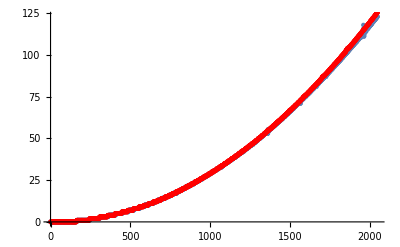

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name1 := "bag"
name2 := "min"
data1 :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name1,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
data2 :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name2,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
Show[ListPlot[data1],ListPlot[data2,PlotStyle->Red]]
```